## Idea

ℰ(t_2)=Λ(t_2,t_1)ℰ(t_1) ⇒ Λ(t_2,t_1)=ℰ(t_2)ℰ^-1(t_1)

## Packages import and definitions

```mathematica
SetDirectory[NotebookDirectory[]]
Get["../Mathematica_packages/QMB.wl"]
Get["../Mathematica_packages/Chaometer.wl"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files

```mathematica
(* Import the superoperators of the three random states of the videos *)
superoperatorsChaotic=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_"<>ToString[#]<>".csv"][[2;;]](*en la posición 1 está guardada la información*)]&/@{1,2,3};
superoperatorsRegular=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/regular/superoperators_"<>ToString[#]<>".csv"][[2;;]](*en la posición 1 está guardada la información*)]&/@{1,3};
```

```mathematica
(* Random check that the superoperators are TP *)
Chop[Total/@Transpose[superoperatorsChaotic[[1,RandomInteger[{1,501}]]]][[All,{1,4}]]]
```

{1.,0,0,1.}

### Plots

```mathematica
specialPointsCoord=Join[#,-#]&[IdentityMatrix[3]];
```

```mathematica
specialPointsColors={Magenta,Orange,Red,Blue,Cyan,Green}
```

{RGBColor[1, 0, 1],RGBColor[1, 0.5, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[0, 1, 0]}

```mathematica
specialPoints={#[[1]],PointSize[0.02],Point[#[[2]]]}&/@Transpose[{specialPointsColors,specialPointsCoord}]
```

{{RGBColor[1, 0, 1],PointSize[0.02],Point[{1,0,0}]},{RGBColor[1, 0.5, 0],PointSize[0.02],Point[{0,1,0}]},{RGBColor[1, 0, 0],PointSize[0.02],Point[{0,0,1}]},{RGBColor[0, 0, 1],PointSize[0.02],Point[{-1,0,0}]},{RGBColor[0, 1, 1],PointSize[0.02],Point[{0,-1,0}]},{RGBColor[0, 1, 0],PointSize[0.02],Point[{0,0,-1}]}}

```mathematica
SpecialPoints[M_,κ_]:={#[[1]],PointSize[0.02],Point[M.#[[2]]+κ]}&/@Transpose[{specialPointsColors,specialPointsCoord}]
```

```mathematica
points=Complement[Flatten[Table[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,Pi/30,Pi-Pi/30,Pi/30},{ϕ,0,2Pi,Pi/30}],1],specialPointsCoord];
```

```mathematica
Graphics3D[{specialPoints,Point/@points}]
```

-Graphics3D-

## Chaotic region

### Parameters setup

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}(*chaotic region*);

(*Diagonalize spin chain Hamiltonian*)
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]

(*Set initial state of environment: Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3][[1]];
```

### Calculation of most negative eigenvalue λ̃ of Λ^R(t_2,t_1)/2

```mathematica
AbsoluteTiming[superoperatorsChaotic=Superoperator[#,ψ0E,eigVals,eigVecs,L]&/@Range[0,10,0.1](*t∈[0,1]*);]
```

{609.946,Null}

```mathematica
Lambdas=Table[#2.Inverse[#1]&@@@Transpose[{#,RotateLeft[#]}&[superoperatorsChaotic[[i]]]][[;;-2]],{i,3}];
```

```mathematica
choiEigenvaluesChaotic=Map[Chop[Eigenvalues[1/2*Reshuffle[#]]]&,Lambdas,{2}];
```

```mathematica
spectralDistanceChoiChaotic=Map[Abs[Min[#]]&,choiEigenvaluesChaotic,{2}];
```

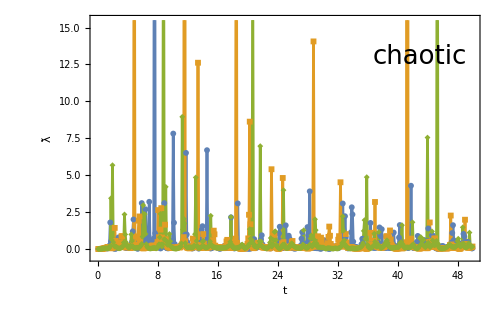

```mathematica
ListPlot[Transpose[{Range[0.1,50,0.1],#}]&/@spectralDistanceChoiChaotic,
PlotRange->{All,{-0.5,15.5}},
Joined->True,PlotMarkers->{Automatic, 6},
Frame->True,
FrameLabel->{"t","λ̃"},
FrameStyle->Directive[Black,FontSize->26,FontFamily->"Arial"],
Epilog->{Text[Style["chaotic",FontSize->26],{43,13}]},
ImageSize->500
]
```

```mathematica
Select[spectralDistanceChoiChaotic[[1]],#>15&]
```

{41.7369}

```mathematica
Position[spectralDistanceChoiChaotic[[1]],%[[1]]]
```

{{76}}

```mathematica
Lambdas[[1,76]]
```

{{7.50497-2.47997×10^-13 ⅈ,-4.44202+0.10703 ⅈ,-4.44202-0.10703 ⅈ,-6.27775+2.65356×10^-13 ⅈ},{19.7792-65.8672 ⅈ,-12.3867+44.9852 ⅈ,-13.513+44.9656 ⅈ,-19.0815+63.5663 ⅈ},{19.7792+65.8672 ⅈ,-13.513-44.9656 ⅈ,-12.3867-44.9852 ⅈ,-19.0815-63.5663 ⅈ},{-6.50497+4.07984×10^-13 ⅈ,4.44202-0.10703 ⅈ,4.44202+0.10703 ⅈ,7.27775-3.74664×10^-13 ⅈ}}

```mathematica
spectralDistanceChoiChaotic[[1,76]]
```

41.7369

## Integrable region

### Parameters setup

```mathematica
superoperators=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/regular/superoperators_1.csv"][[2;;]](*en la posición uno está guardada la información*)];
```

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]}(*chaotic region*);

(*Diagonalize spin chain Hamiltonian*)
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=N[Chop[Eigensystem[H]]];
]

(*Set initial state of environment: Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3][[1]];
```

### Calculation of most negative eigenvalue λ̃ of Λ^R(t_2,t_1)/2

```mathematica
AbsoluteTiming[superoperatorsRegular=Superoperator[#,ψ0E,eigVals,eigVecs,L]&/@Range[0,10,0.1](*t∈[0,1]*);]
```

{431.576,Null}

```mathematica
Lambdas=Table[#2.Inverse[#1]&@@@Transpose[{#,RotateLeft[#]}&[superoperatorsRegular[[i]]]][[;;-2]],{i,3}];
```

```mathematica
choiEigenvaluesRegular=Map[Chop[Eigenvalues[1/2.Reshuffle[#]]]&,Lambdas,{2}];
```

```mathematica
spectralDistanceChoiRegular=Map[Abs[Min[#]]&,choiEigenvaluesRegular,{2}];
```

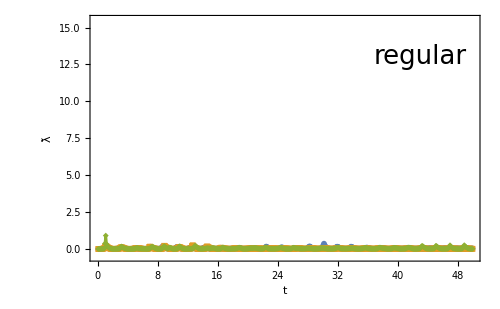

```mathematica
ListPlot[Transpose[{Range[0.1,50,0.1],#}]&/@spectralDistanceChoiRegular,
PlotRange->{All,{-0.5,15.5}},
Joined->True,PlotMarkers->{Automatic, 6},
Frame->True,
FrameLabel->{"t","λ̃"},
FrameStyle->Directive[Black,FontSize->26,FontFamily->"Arial"],
Epilog->{Text[Style["regular",FontSize->26],{43,13}]},
ImageSize->500
]
```

```mathematica
choiEigenvaluesRegular[[2,11]]
```

{3.74543,-1.81994,0.099944,-0.0254347}

```mathematica
Sqrt@Eigenvalues[ConjugateTranspose[#].#&[(Reshuffle[Lambdas[[2,11]]])]]
```

{3.74543,1.81994,0.099944,0.0254347}

```mathematica
Reshuffle[Lambdas[[2,11]]]//Eigenvalues
```

{3.74543,-1.81994,0.099944,-0.0254347}

## Geometric picture of what happens in λ̃ bursts

```mathematica
canonicalStates=Dyad[Normalize[Eigensystem[Pauli[#]][[2,2]]]]&/@{1,2,3};
```

```mathematica
(* For the first random state, let us see what happens from 7.5s to 7.6s *)
{i,t1,t2}={1,7.5,7.6}(* i: random state *);
Table[
κ=BlochVector[ArrayReshape[superoperatorsChaotic[[1,t/0.1+1]].{1/2,0,0,1/2},{2,2}]](* origin displacement *);
M=Transpose[BlochVector[ArrayReshape[superoperatorsChaotic[[1,t/0.1+1]].Flatten[#],{2,2}]]-κ&/@canonicalStates](* affine transformation of the Bloch sphere *);
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},0.17]},Point[M.#+κ]&/@points,SpecialPoints[M,κ]},
ImageSize->400,Axes->True,
AxesLabel->{x,y,z},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->20]]
,{t,t1,t2,0.1}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Module[{t=t1},
κ=BlochVector[ArrayReshape[superoperatorsChaotic[[1,t/0.1+1]].{1/2,0,0,1/2},{2,2}]](* origin displacement *);
M=Transpose[BlochVector[ArrayReshape[superoperatorsChaotic[[1,t/0.1+1]].Flatten[#],{2,2}]]-κ&/@canonicalStates](* affine transformation of the Bloch sphere *);
pointsBeforeBurst=M.#+κ&/@points;
]
```

```mathematica
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},0.17]},Point[pointsBeforeBurst],SpecialPoints[M,κ]},
ImageSize->400,Axes->True,
AxesLabel->{x,y,z},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->20]]
```

-Graphics3D-

```mathematica
MatrixForm[LambdaBeforeBurst=Chop[superoperatorsChaotic[[1,t2/0.1+1]].Inverse[superoperatorsChaotic[[1,t1/0.1+1]]]]]
```

(7.50497 | -4.44202+0.10703 ⅈ | -4.44202-0.10703 ⅈ | -6.27775
19.7792-65.8672 ⅈ | -12.3867+44.9852 ⅈ | -13.513+44.9656 ⅈ | -19.0815+63.5663 ⅈ
19.7792+65.8672 ⅈ | -13.513-44.9656 ⅈ | -12.3867-44.9852 ⅈ | -19.0815-63.5663 ⅈ
-6.50497 | 4.44202-0.10703 ⅈ | 4.44202+0.10703 ⅈ | 7.27775)

```mathematica
Chop[Eigenvalues[1/2.*Reshuffle[LambdaBeforeBurst]]]
```

{42.1886,-41.7369,40.9161,-40.3678}

```mathematica
{κBurst=BlochVector[ArrayReshape[LambdaBeforeBurst.{1/2,0,0,1/2},{2,2}]],
SingularValueList[MBurst=Transpose[BlochVector[ArrayReshape[LambdaBeforeBurst.Flatten[#],{2,2}]]-κBurst-κ&/@canonicalStates]]}
```

{{0.697731,2.30093,0.227217},{165.209,1.0085,0.259321}}

```mathematica
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},0.17]},Point[MBurst.#+κBurst]&/@pointsBeforeBurst,SpecialPoints[M,κ]},
ImageSize->400,Axes->True,
AxesLabel->{x,y,z},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->20]]
```

-Graphics3D-

```mathematica
Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},1]},Point[MBurst.#+κBurst]&/@points,SpecialPoints[MBurst,κBurst]},
PlotRange->Table[{-165,165},3],
ImageSize->400,Axes->True,
AxesLabel->{x,y,z},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->20]]
```

-Graphics3D-

## sfd

```mathematica
1/2{{1,2/(√2)-I 2/(√2)},{2/(√2)+I 2/(√2),1}}//Eigenvalues
```

{3/2,-1/2}

```mathematica
Eigenvalues[{{1+z,x+ⅈ y},{x-ⅈ y,1-z}}/2]
```

{1/2 (1-√(x^2+y^2+z^2)),1/2 (1+√(x^2+y^2+z^2))}

```mathematica
Limit[Exp[-I (a-b)t],t->∞]
```

lim_(t→∞) ⅇ^(-ⅈ (a-b) t)

```mathematica
Exp[-I (1-2)1000.]//Re
```

0.562379